```mathematica
gauss[x_]:= A * Exp[-(x-x0)^2/(2*σ^2)]
gauss''''[x]
gauss'[x]
g [x_]:=gauss'[x]
f[x_]:=gauss'[x]
g [x_]:=gauss[x]/.{A->5,σ->10,x0->10}
f[x_]:=gauss[x]/.{A->10,σ->10,x0->-10}
add[x_]:=f[x]+g[x]

Plot[{g[x],f[x], f[x]+g[x]},{x,-30,30}]
Plot[g'[x],{x,-30,30}]
Plot[f'[x],{x,-30,30}]
Plot[add''''[x], {x,-30,30}]
```

(A ⅇ^(-(x-x0)^2/(2 σ^2)) (x-x0)^4)/σ^8-(6 A ⅇ^(-(x-x0)^2/(2 σ^2)) (x-x0)^2)/σ^6+(3 A ⅇ^(-(x-x0)^2/(2 σ^2)))/σ^4

-(A ⅇ^(-(x-x0)^2/(2 σ^2)) (x-x0))/σ^2

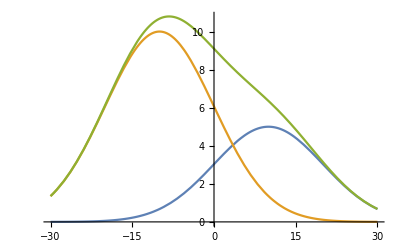

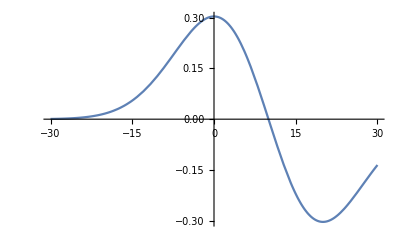

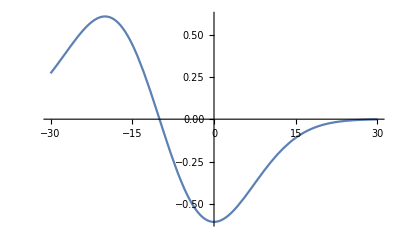

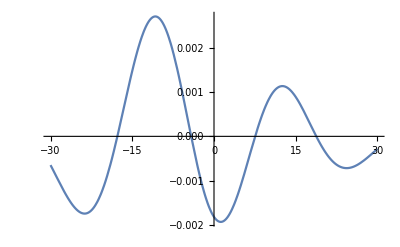

```mathematica
print x[1]-x[0]
```